```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Metal SPR\\alcohol.xlsx"]
```

```mathematica
data3={{65.,861.6666666666666},{66.,855.},{67.,849.3333333333334},{68.,847.3333333333334},{69.,832.6666666666666},{70.,810.6666666666666},{71.,789.3333333333334},{72.,690.3333333333334},{73.,538.6666666666666},{74.,325.6666666666667},{74.5,191.},{75.,117.66666666666667},{75.5,71.},{76.,79.33333333333333},{77.,189.66666666666666},{78.,324.6666666666667},{79.,476.3333333333333},{80.,575.3333333333334},{81.,624.}}
```

{{65.,861.667},{66.,855.},{67.,849.333},{68.,847.333},{69.,832.667},{70.,810.667},{71.,789.333},{72.,690.333},{73.,538.667},{74.,325.667},{74.5,191.},{75.,117.667},{75.5,71.},{76.,79.3333},{77.,189.667},{78.,324.667},{79.,476.333},{80.,575.333},{81.,624.}}

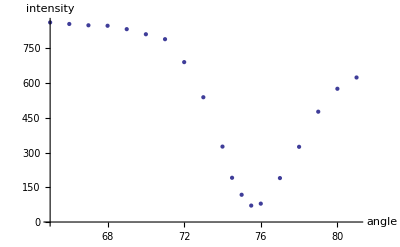

```mathematica
Show[ListPlot[data3],AxesLabel-> {"angle","intensity"}]
```

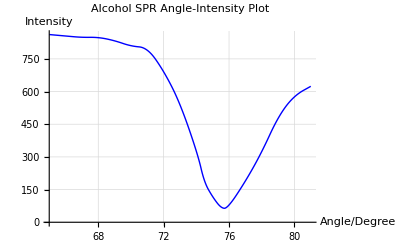

```mathematica
gra=ListLinePlot[data3,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Angle/Degree","Intensity"},PlotLabel->"Alcohol SPR Angle-Intensity Plot",GridLines->Automatic]
```